```mathematica
(*Importing steady-state for κ=0.2, g=1.5*)
κ=0.2;
g=1.5;
Get["/Users/zoe/Documents/Wolfram Mathematica/fig1_phiss_g1p5_k0p2"];
Phi0p2=Interpolation[FinalPhiList,InterpolationOrder->4];
ϕss0p2[x_]:=Phi0p2[(π^(1/2)*Exp[(2  π*κ)^(1/2)  x])/(1+Exp[(2  π*κ)^(1/2)  x])];
data=Table[{x,ϕss0p2[x]},{x,-50,50,0.001}];
ϕssint=Interpolation[data];
intermediatePhi[x_]:=2*Sqrt[π]*ϕssint[x];
cosTerm[x_]:=Cos[intermediatePhi[x]];
potentialhamiltonian[x_]:=2*Pi*κ*cosTerm[x]+g^2;
```

InterpolatingFunction::dmval: Input value {8.06134×10^-25} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {8.07038×10^-25} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {8.07944×10^-25} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
(*Finding eigenvalues and eigenfunctions of quadratic theory*)
L=100;
dx=.05;
total=50;
H1=-u''[x]+Evaluate[potentialhamiltonian[x]]*u[x];
{vals,fns}=NDEigensystem[{H1,DirichletCondition[u[x]==0,True]},u[x],{x,-L/2,L/2},total,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->dx}},"Arnoldi","MaxIterations"->7000,"BasisSize"->total+1,"Shift"->2.8}];
```

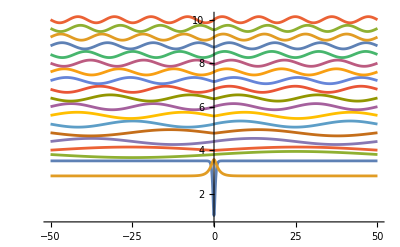

```mathematica
(*The bound eigenfunction's y value corresponds to its eigenvalue so it looks more accurate next to the potential well, but the scattering state's y value is just chosen so its above the potential but they dont overlap so you can see them clearly.  minus signs are added to give the same sign convention to each eigenfunction*)
efunsplot=Plot[{potentialhamiltonian[x],fns[[1]]+vals[[1]],fns[[2]]+3.8,fns[[3]]+4,fns[[4]]+4.4,fns[[5]]+4.8,-fns[[6]]+5.2,-fns[[7]]+5.6,-fns[[8]]+6,-fns[[9]]+6.4,fns[[10]]+6.8,fns[[11]]+7.2,-fns[[12]]+7.6,fns[[13]]+8,-fns[[14]]+8.4,-fns[[15]]+8.8,fns[[16]]+9.2,fns[[17]]+9.6,fns[[18]]+10},{x,-50,50},PlotRange->{{-50,50},{.7,10.15}}]
```

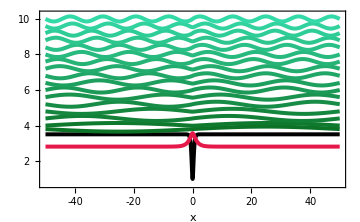

```mathematica
(*Pretty figure*)

col0=Black; (*color of potential*)
col1=RGBColor[.902,.097,.294]; (*color of bound eigenfunction*)
gradCols=Table[Blend[{RGBColor[0.05,0.45,0.15],RGBColor[0.20,0.85,0.65]},i/16],{i,0,16}]; (*color gradient of scattering eigenfunctions*)

allStyles=Join[{{col0,Thickness[0.008]}},{{col1,Thickness[0.008]}},Table[{gradCols[[i]],Thickness[0.008]},{i,1,17}]];

efunsplot=Plot[{potentialhamiltonian[x],fns[[1]]+2.81517,fns[[2]]+3.8,fns[[3]]+4,fns[[4]]+4.4,fns[[5]]+4.8,-fns[[6]]+5.2,-fns[[7]]+5.6,-fns[[8]]+6,-fns[[9]]+6.4,fns[[10]]+6.8,fns[[11]]+7.2,-fns[[12]]+7.6,fns[[13]]+8,-fns[[14]]+8.4,-fns[[15]]+8.8,fns[[16]]+9.2,fns[[17]]+9.6,fns[[18]]+10},{x,-50,50},PlotStyle->allStyles,PlotRange->{{-50,50},{0.7,10.25}},Axes->False,Frame->True,FrameStyle->Directive[Black,Thickness[0.001]],FrameTicks->{{None,None},{{{-40,"-40"},{-20,"-20"},{0,"0"},{20,"20"},{40,"40"}},None}},FrameLabel->{Style["x",Italic,14],None },FrameTicksStyle->Directive[Black,12],BaseStyle->{FontFamily->"Times New Roman",FontSize->12},ImageSize->5*72,ImagePadding->{{55,15},{40,15}},Background->White]
```